# 总结

1. Mathematica .nb笔记本的使用：
   - 支持多种样式，可用于编写代码和做笔记。
   - 基本操作介绍，包括单元类型的选择、代码计算的方法等。

2. 数学表达式的输入和处理：
   - 如何在 Mathematica 中输入和处理复杂数学表达式的示例。
   - 快捷键的使用，如输入根号、上下标、分数等。

3. 编程和代码结构：
   - Mathematica 中的编程结构，不需要像C使用 `#include` 或 `int main()` 等。
   - `ClearAll` 函数的用途，以及如何用它清除全局命名空间中的定义。

4. 符号计算和数学函数的使用：
   - 如何进行符号计算，并介绍多种内置数学函数，如 `FullSimplify`、`CoefficientList` 等。

5. 图形绘制：
   - 展示了如何使用 Mathematica 绘制图形，如正弦函数的平方图。

6. 特殊输入模式：
   - 使用等号开头的特殊输入模式，如自然语言输入或 Wolfram Alpha 查询。

7. 控制结构和循环：
   -  `For` 和 `While` 循环的使用，以及如何高效地处理大量数据。

8. 函数式编程：
   - 纯函数和 `Map` 函数的用法，包括如何将函数应用于列表的每个元素。

9. 数据结构操作：
   - 操作和转换数组和列表，如使用 `Flatten`、`Join` 等函数。

10. 条件和逻辑操作：
    -  `If` 语句的使用，类似于 C 中的条件（三元）运算符。
    
    完整代码见 https://github.com/chenyu76/MyMathematicaNotebook

# 1.

Mathematica 笔记本支持不同的样式，除了写代码之外你也可以用它来做笔记

## Mathematica 图形界面的一些基本操作

### 在候选框里可以选择当前单元的类型

如果你直接输入而不选择类型，默认是Input单元，对于一个Input单元，你可以按下 Shift+Enter 计算，或者如果想计算整个笔记本的所有Input，可以按 菜单栏-计算-计算笔记本，你也可以在这里控制目前的计算，比如停止计算等

### 配合一些快捷键可以打出比较好看的公式

在C中，我们进行一些复杂的数学运算的时候，可能会出现这种情况：

A = (A1/pow(p - k1,2) + A2/pow((p - k2),2) + 12*p*p - 1)*pow((p - k1),2) *pow((p -  k2),2);

不是很美观

但是在 Mathematica里我们可以打出

A=(A1/(p- k1)^2+A2/(p- k2)^2+12 p^2-1)(p- k1)^2(p- k2)^2;

并且这是可以直接参与计算的，有效的Mathematica代码

#### 常用输入快捷键

- Ctrl + 4 :  内嵌 输入
- Ctrl + 2 : √根号
- Ctrl + 6 : 上标^这是上标 
- Ctrl + -  : 下标_这是下标
- Ctrl + /  :  分数/这是分母
- Esc :  按下Esc再输出符号名称再按下Esc，可以打出希腊字母或其他符号，比如Esc+a l p h a+Esc可以输入 α ，可以使用Tab自动补全
- =: 在Mathematica中，在行的开头使用等号启动了一种特殊的输入模式，称为自然语言输入或Wolfram Alpha查询。这种输入方式允许你使用自然语言提出问题或指令，Mathematica会尝试解释这个输入并给出一个有意义的结果

WolframAlphaQueryParseResults

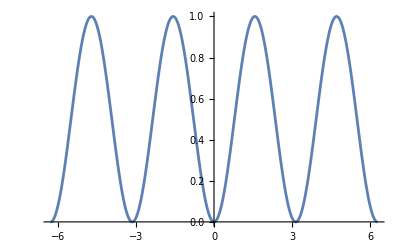

WolframAlphaQueryResults

42

### 代码的开始

在Mathematica中，我们一般不用像C一样进行#include,内置的函数一般情况下都是能满足需求的，也不需要使用

int main(){

return 0;
}

来框定主程序范围

和C不同，在Mathematica定义的所有符号在程序运行完后都会保留，直到你关闭所有的Mathematica窗口，所以在每个程序开头的时候执行这条语句是有必要的，这可以避免在某些情况下产生的符号定义问题：

```mathematica
ClearAll["Global`*"]
```

语句用于清除在全局命名空间中定义的所有符号的值、定义、属性等。这重置你的工作环境到一个干净的状态
“Global*”是一个模式，匹配全局命名空间中的所有符号。
你也可以传递别的参数给 ClearAll 以清除指定的符号，比如， ClearAll[x] 可以清除符号x的所有属性.


首先通过 = 将=右边的值赋给A,在之后调用A时，它的值便是右边的那一串

注意到A1, p, k1等值没有定义过，在其他语言肯定会报错，这是Mathematica符号计算能力的体现，你可以先使用符号但是不定义它，等以后再来定义
注意12和p之间有空格，这是隐式的乘法写法，12 p 和12*p是等价的

```mathematica
A=(A1/(p- k1)^2+A2/(p- k2)^2+12 p^2-1)(p- k1)^2(p- k2)^2;
Coe1=CoefficientList[%,p]//FullSimplify
Expand[12(x-(a1+I *b1))^2(x-(a1-I *b1))^2(x-(a2+I *b2))(x-(a2-I*b2)),x];
Coe2=FullSimplify[CoefficientList[%,x]]
(* 使用（* *）包裹的是注释，代码可以使用快捷键Shift+Enter 运算，注释会被跳过 *)
```

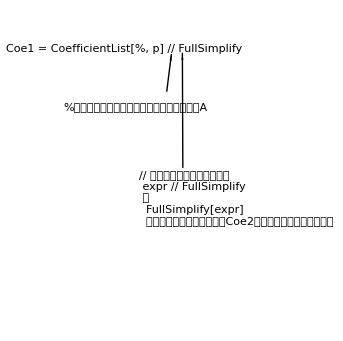
-Graphics-
这里的FullSimplify, I和CoefficientList都是内置符号，内置符号均以大写字母开头,所以写作I但是其实是，虚数单位

四条语句只有两条输出：另外两条语句使用了;抑制输出

分号（;）作用：
1. 分隔命令:
分号用于在同一行或表达式中分隔多个命令。这允许你在一个输入单元中编写并执行多个命令， 而不需要将它们放在不同的行或单元中。每个通过分号分隔的命令会按顺序被评估。
2. 抑制输出:
当分号用于一个表达式的末尾时，它会抑制该表达式的输出。通常，Mathematica会显示最后一个表达式的结果。通过在命令的末尾添加分号，你可以阻止这个结果的显示。

FullSimplify
在Mathematica中，FullSimplify[expr]函数用于尝试将表达式expr简化到最简形式。比如，FullSimplify[44/14]的结果会是 22/7
此外，还有Simplify函数也可以简化表达式，但它使用的规则和变换比FullSimplify少，因此在某些情况下可能不会找到尽可能简化的形式，但运算会更快

CoefficientList
在Mathematica中，CoefficientList函数是用于从多项式表达式中提取系数并将它们以列表的形式返回的工具。

例如，考虑多项式3 x^2 + 2 x + 1，你可以使用CoefficientList来提取其系数：

CoefficientList[3 x^2 + 2 x + 1,x]

将返回{1,2,3},分别对应于x^0、x^1 和x^2 的系数。

CoefficientList也能够处理多变量的情况,例如CoefficientList[3 x^2 y+2 x y^2+y,{x,y}]将返回一个二维列表，每个元素对应于x和y的不同幂次的系数。

```mathematica
C15=Coe1[[5]]/.{k2->-k1,a1->-1/2*a2}
C25=Coe2[[5]]/.{k2->-k1,a1->-1/2*a2}//FullSimplify
Solve[C15==C25,b1]//FullSimplify
```

-1-24 k1^2

{6 (-3 a2^2+4 b1^2+2 b2^2)}

C15 = Coe1[[5]] /. {k2 -> -k1, a1 -> -1/2*a2}

Coe1[[5]] ：这部分代码从列表Coe1中提取第5个元素。在Mathematica中，列表的索引从1开始。然后使用=将其赋给C15

/. 是Mathematica中的替换操作符（ReplaceAll函数的简写），用于在表达式中替换一些特定的规则。它的作用是在其左边的表达式中查找并替换所有匹配右侧规则列表中模式的实例。

{k2 -> -k1, a1 -> -(1/2)*a2}是一个规则列表，其中包含两条替换规则：
    k2 -> -k1：这条规则表示所有k2被替换为-k1。
    a1 -> -(1/2)*a2：这条规则表示所有a1被替换为-(1/2)*a2。
    
Solve 函数

在Mathematica中，Solve函数用于求解方程或方程组。你可以用它来找到一个或多个变量的解，使得给定的方程或方程组成立。

Solve函数的基本用法是Solve[eqns, vars]，其中eqns是要解决的方程或方程组，vars是需要解决的变量列表。Solve会尝试找到满足方程（组）的vars的所有可能值。

 例如

```mathematica
Solve[x^2 + a x + 1 == 0, x]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

注意是==而不是=

```mathematica
C14=Coe1[[4]]/.{k2->-k1,a1->-1/2*a2}/.{b1->1/2 √(-1/6+3 a2^2-2 b2^2-4 k1^2)}//FullSimplify
C24=Coe2[[4]]/.{k2->-k1,a1->-1/2*a2}/.{b1->1/2 √(-1/6+3 a2^2-2 b2^2-4 k1^2)}//FullSimplify
Solve[C14==C24,a2]//FullSimplify
```

```mathematica
{b1->1/2 √(-1/6+3 a2^2-2 b2^2-4 k1^2)}/.{a2->1/2 √(1/6+6 b2^2+4 k1^2)}/.{b2->-(√(-1+96 k1^2))/(2 √15)}//FullSimplify
```

{b1→1/4 √(-1/3+12 k1^2)}

新函数 出现了!

```mathematica
Reduce[1/4 √(-1/3+12 k1^2)>0,k1,Reals]
```

k1<-1/6||k1>1/6

Reduce
它寻找并给出一个或多个变量满足给定条件的所有可能的解。与Solve函数相比，Reduce提供了更为全面和详细的解的描述，能够处理更复杂的数学结构，并且能够给出更加完整的解的条件。

基本用法
Reduce函数的基本用法是Reduce[expr, vars]，其中expr可以是一个方程、不等式或它们的系统，vars是需要解决的变量或变量列表。
当你需要将解限定在某个域内时，增加一个参数，调用 Reduce[expr,vars,dom] , 表示在域 dom 上的约化. dom 的选取通常是 Reals、Integers 和 Complexes. 
Solve 也可以增加dom参数控制域.

```mathematica
Solve[x^2 + a x + 1 == 0, x, Reals]
```

{{x→ConditionalExpression[-a/2-1/2 √(-4+a^2), a>2||a<-2]},{x→ConditionalExpression[-a/2+1/2 √(-4+a^2), a>2||a<-2]}}

特点
    全面性：Reduce尝试找到给定条件下变量的所有可能解，并且能处理方程、不等式及它们的组合。
    条件解：Reduce不仅给出解，还能提供解成立的条件，这对于不等式尤其有用。
    逻辑表达式：Reduce的结果通常是一个逻辑表达式，包括And、Or、Not等，清晰地描述了解的条件和范围。
    
与Solve的比较

虽然Solve和Reduce在许多情况下都可以用来求解方程和不等式，但Reduce在处理包含不等式的系统或需要详细解的条件时，尤其有用。Solve侧重于求解方程，直接给出解的形式，而Reduce提供了一个更全面的解决方案，包括所有可能的解和这些解满足的条件。

```mathematica
Solve[x^2 + a x + 1 > 0, x]
```

Solve::fdimc: 当参数值满足条件 a>2||a>2||a<-2||a<-2||-2<a<2 时，解集包含一个完全维度的分量；请使用 Reduce 获取全部解的信息.

{}

```mathematica
Reduce[x^2 + a x + 1 > 0, x]
```

x∈ℝ&&((a≤-2&&(x<-a/2-1/2 √(-4+a^2)||x>-a/2+1/2 √(-4+a^2)))||-2<a<2||(a≥2&&(x<-a/2-1/2 √(-4+a^2)||x>-a/2+1/2 √(-4+a^2))))

```mathematica
Parameter0={k1->1,k2->-1,A1->(10902-779 √123)/144,A2->(10902+779 √123)/144};
Parameter0//N
A=(-A1/(p- I*k1)^2-A2/(p-I*k2)^2-12*p^2-1)/.Parameter0;
Solve[A==0,p]//Simplify
% //N
```

N[expr]
给出 expr 的数值值.

N[expr,n]
尝试给出具有 n 位精度的结果.

```mathematica
N[Pi]
N[Pi,3]
N[Pi,10]
```

3.14159

3.14

3.141592654

```mathematica
{κ1,κ2,ϵ1,ϵ2,ρ1,ρ2}={1,-1,1,1,Sqrt[(10902-779 √123)/144],Sqrt[(10902+779 √123)/144]};
```

将右边列表的第n个值依次赋给左边列表的第n个值，左右两边长度需要相同

```mathematica
{Var1, Var2} = {1, 2, 3};
{Var1, Var2}
```

Set::shape: 列表 {Var1,Var2} 和 {1,2,3} 形状不同.

{Var1,Var2}

= 和 := (Set 和 SetDelayed)
在Mathematica中，`=`和`:=`是两种不同的赋值操作符，它们在函数定义和变量赋值时有着根本的区别：

=（Set）
=用于立即赋值操作。当使用=时，Mathematica会立即计算右侧表达式的值，并将这个值赋给左侧的变量或函数名。
这意味着，无论何时引用这个变量或函数，你都会得到当初赋值时计算得到的结果。

例如：
x = 2 + 3
执行后，x的值将被设置为5，之后无论何时调用x，它都代表5。

Tips:
=是Set[ , ] 的简写，
Set[x, 2+3]
和上面那行程序是等价的

:=（SetDelayed）

:=用于延迟赋值操作。当使用:=时，右侧的表达式不会立即计算，而是每次在调用变量或函数时计算。
- 这意味着，表达式的值会根据其被调用时的环境动态变化。

例如：
y := 2 + 3
这里，表达式2 + 3不会立即计算。每次使用y时，2 + 3都会被重新计算。

```mathematica
F[p_]:=(ϵ1 ρ1^2)/(p-I κ1)+(ϵ2 ρ2^2)/(p-I κ2)-4 p^3-p;
Series[F[p[κ]]-F[p[0]]/3 ( Exp[κ]+2Exp[-κ/2]*Cos[Sqrt[3]/2 κ]),{κ,0,10}];
(*                       Exp[ ],Cos[ ], Sqrt[ ] 等等都是有的，注意要大写 Exp[x] == E^x *)
Coe=CoefficientList[%,κ]/.{p[0]->1/12 (√105+ⅈ √123)}//Simplify;
```

```mathematica
Solve[{Coe[[4]]==0,Coe[[5]]==0,Coe[[6]]==0,Coe[[7]]==0,Coe[[8]]==0},{ p'[0], p''[0],Derivative[3][p][0],Derivative[4][p][0],Derivative[5][p][0]}]//Simplify
```

Series[f,{x,x_0,n}]
生成 f 关于点 x = x_0 的幂级数展开式，最高次数为 ( x - x_0 )^n，其中 n 是显式整数.

```mathematica
Series[Exp[x], {x, 0, 5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

如果你不希望见到高阶无穷小量，使用Normal转换为普通表达式：

```mathematica
Normal[%]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

Solve
方程组写法：列表

```mathematica
Solve[{x+ y==2, x-y==0}, {x,y}]
```

{{x→1,y→1}}

# 2.

Table
 Table[expr,n]
产生 expr 的 n 个拷贝的列表.

```mathematica
Table[i, 10]
```

{i,i,i,i,i,i,i,i,i,i}

Table[expr,{i,i_max}]
产生 i 从1到 i_max 的 expr 值的列表.

```mathematica
Table[i^2, {i, 10}]
Table[x[i],{i,10}]
Table[x[i] -> XXX[[i]], {i,12}]
```

Table[expr,{i, i_min, i_max}]
从 i=i_min 开始.

```mathematica
Table[i^2, {i,4,10}]
```

{16,25,36,49,64,81,100}

Table[expr,{i, i_min, i_max, d_i}]
使用步长 d_i .

```mathematica
Table[i^2, {i,4,10,2}]
```

{16,36,64,100}

Table[expr,{i,{ i_1, i_2,…}}]
使用连续值 i_1、i_2、…

Table[expr,{i, i_min, i_max},{j, j_min, j_max},…]
给出一个嵌套列表. 和 i 相关联的列表是最外的列表.

```mathematica
Table[10i + j, {i,4},{j,4}]
```

{{11,12,13,14},{21,22,23,24},{31,32,33,34},{41,42,43,44}}

```mathematica
MatrixForm[%];
```

(11 | 12 | 13 | 14
21 | 22 | 23 | 24
31 | 32 | 33 | 34
41 | 42 | 43 | 44)

Sum
 Sum[f,{i,i_max}]
求和式 的值.

```mathematica
Sum[i, {i, 100}]
```

5050

```mathematica
∑_(i=1)^100 i
```

5050

```mathematica
Sum[1/i^2,{i, Infinity}]
```

π^2/6

Sum[f,{i,imin,imax}]
从  开始求值.

Sum[f,{i,imin,imax,di}]
使用步长 di 求值.

Sum[expr,{i,{i1,i2,…}}]
用连续值 i1,i2, … .

Sum[f,{i,imin,imax},{j,jmin,jmax},…]
求多重和式的值.

Sum[f,i]
给出不定和 .

While[test,body]
重复计算 test，然后是 body，直到 test 第一次不能给出 True.

```mathematica
i = 1;
While[i!= 10,
	Print[i];
	i++;
];
```

用逗号作为 While 的各个部分的分隔符，用分号作为程序各个部分的分隔符

For[start,test,incr,body]
执行 start，然后重复计算 body 和 incr，直到 test 不能给出 True.

```mathematica
For[i=1,i<10,i++,
	Print[i];
];
```

在Mathematica中(和MATLAB)，由于底层的设计不同，For / While循环要比C/C++中的慢上许多，所以在处理数组时，建议避开直接使用循环遍历

作为一种高级编程语言，其设计强调函数式编程和规则替换，这些范式旨在提高代码的简洁性和效率

以将一个列表中每个元素加1为例：

```mathematica
testList = Table[i, {i,10^6}];
AbsoluteTiming[For[i=1,i<=Length[testList],i++,testList[[i]] += 1;]][[1]]
(*                                                        只取第一个元素
AbsoluteTiming[expr]返回一个列表，其中第一个元素是expr开始执行到完成所经过的实际时间用于执行的秒数，第二个元素是expr的执行结果。 *)
testList = Table[i, {i,10^6}];
AbsoluteTiming[ Table[i+1,{i,testList}] ][[1]]
testList = Table[i, {i,10^6}];
AbsoluteTiming[ Map[Function[var, var+1],testList] ][[1]](*  #+1& /@ testList *)
testList = Table[i, {i,10^6}];
AbsoluteTiming[ testList+1 ][[1]]
```

1.41082

0.012127

0.013015

0.000545

Function 纯函数/匿名函数
基本概念
纯函数是一种没有副作用^[1]的函数，它总是在给定相同输入的情况下产生相同的输出。在C语言中，你可能习惯了使用函数来执行某些任务或计算，同时也可能会修改全局状态或依赖于之。相比之下，Mathematica中的纯函数严格遵循输入到输出的映射，不依赖于也不修改任何外部状态。

[1]: 在编程领域，“副作用”（Side Effects）指的是函数或表达式在计算结果的同时，对外部环境或状态造成的改变。这些改变可以包括修改全局变量、更改对象的成员、进行输入/输出操作（如打印到控制台、读写文件），或者是调用其他具有副作用的函数。副作用使得一个函数的行为不仅仅依赖于其输入参数，还依赖于外部状态或它对外部状态的改变。

创建纯函数
在Mathematica中，纯函数通常是通过`Function`关键字或`#`和`&`符号来创建的。比如，一个将输入乘以2的纯函数可以写作：
Function[x, 2*x]

或者使用更简洁的符号：
#*2 &
这里，`#`代表函数的参数，`&`标记了纯函数的结束。

使用纯函数
纯函数可以立即应用于输入值。例如，(#+3)&[5]将输出8。这与C中调用函数类似，但注意到这里函数是匿名的，直接在其上应用参数，更为简洁。

这个函数和C这样写是类似的：

// 定义函数
int add3(int i){
    return i + 3;
}
// 调用函数
add3[5];

Map & MapAt
Map( /@ )
`Map`函数在Mathematica中用于将一个函数应用于列表（或其他集合）中的每个元素。在C语言中，这类似于使用循环遍历数组并对每个元素执行某种操作。不过，与C不同的是，`Map`是一种更高级的抽象，它不需要显式的循环结构，也不直接操作数组的索引。可以简写为 /@

示例:
Map[f, {a, b, c}]
这将对列表{a, b, c}中的每个元素应用函数`f`，结果是{f[a], f[b], f[c]}。

MapAt
`MapAt`函数则更加具体，它允许你只对列表中特定位置的元素应用函数。这在C语言中类似于对数组的特定元素执行操作，但是`MapAt`提供了一种更简洁和直接的方式来实现这一点，而不需要使用条件语句来检查索引。

示例:
MapAt[f, {a, b, c}, 2]
这将仅对列表{a, b, c}中位置2的元素（即`b`）应用函数`f`，结果是{a, f[b], c}。

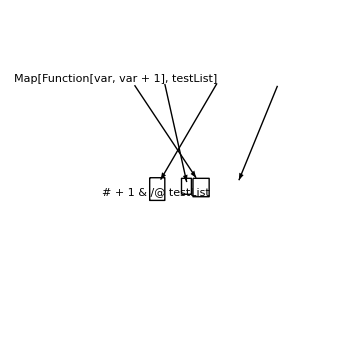

导数 D 
 D[f,x]
给出偏导数 .

```mathematica
D[x^n,x]
```

n x^(-1+n)

D[f,{x,n}]
给出高阶导数 .

```mathematica
D[Sin[x],{x,4}]
```

Sin[x]

D[f,x,y,…]
给出偏导数 .

D[f,{x,n},{y,m},…]
给出高阶偏导数.

D[f,{{x1,x2,…}}]
给出标量 f 的向量导数 .

D[f,{array}]
给出数组导数.

# 3.

Flatten
 Flatten[list]
压平嵌套列表.

```mathematica
Flatten[{{a,b},{c,{d},e},{f,{g,h}}}]
```

{a,b,c,d,e,f,g,h}

Flatten[list,n]
压平 n 层结构.

```mathematica
Flatten[{{a,b},{c,{d},e},{f,{g,h}}},1]
```

{a,b,c,{d},e,f,{g,h}}

Flatten[list,n,h]
压平头部为 h 的子表达式.

Flatten[list,{{s11,s12,…},{s21,s22,…},…}]
通过组合所有级别 sij 压平 list 使每个级别 i 都在结果中.

Values
在规则列表或关联中给出由值组成的列表.

```mathematica
Values[{a->1,b->2,c->3}]
```

{1,2,3}

```mathematica
Values[<|a->1,b->2,c->3|>]
```

{1,2,3}

Count
Count[list,pattern]
给出 list 中匹配 pattern 的元素个数.

```mathematica
Count[{a,a,a,a,b,b,b,c,c,d},a]
```

4

Count[expr,pattern,levelspec]
给出匹配 pattern 的子表达式的总个数，这些子表达式出现在 expr 中由 levelspec 指定的层上.

Count[pattern]
表示可以应用于表达式的 Count 的运算符形式.

Array[f,n,{a,b}]
生成使用 n 个从 a 到 b 的数值组成的列表.

Array[f,{n1,n2,…}]
生成嵌套列表的 n1×n2×… 数组，元素为 f[i1,i2,…].

```mathematica
Array[f,{3,2}]
```

{{f[1,1],f[1,2]},{f[2,1],f[2,2]},{f[3,1],f[3,2]}}

Array[f,{n1,n2,…},{r1,r2,…}]
生成一个列表，该列表使用指标起点 ri (缺省为 1).

Array[f,{n1,n2,…},{{a1,b1},{a2,b2},…}]
生成使用 ni 个从 ai 到 bi 的数值组成的列表.

Array[f,dims,origin,h]
对数组的每一层使用头部 h，而不是 List.

If
If[condition,t,f]
如果 condition 计算为 True 则给出 t，若计算为 False 则给出 f.  
( f 可以省略，此时当condition为False没有返回值)

If[condition,t,f,u]
如果 condition 既不计算为 True 也不计算为 False 则给出 u.

（一般）总是会有返回值
更类似于C中的？三元运算符
condition ? t : f 
而不是
if (condition) {
    t;
} else {
    f;
}

Join
 Join[list1,list2,…]
把列表或其它享有相同头部的表达式连接在一起.

Join[list1,list2,…,n]
连接每个 list_i 的第 n 层的对象.

```mathematica
Join[{a,b,c}, {d,e}]
```

{a,b,c,d,e}

二维作图
Plot[f,{x,xmin,xmax}] 								一维函数f[x]在区间[xmin,xmax]上的函数曲线
Plot[,f2.{f1.},{x,xmin,xmax}] 							在一张图上画几条曲线
ListPlot[{y1,y2,..}]									绘出由离散点对(n,yn)组成的图
ListPlot[{{x1,y1},{x2,y2},..}] 							绘出由离散点对(xn,yn)组成的图
PlarametricPot[{fx,fy},{t,tmin,tmax}] 					由参数方程在参数变化范围内的曲线
ParametricPlot[{{fx,fy},{gx,gy},…},{t,tmin,tmax}]			在一张图上画多条参数曲线
选项：
PlotRange->{0,1} 									作图显示的值域范围
AspectRatio->1/GoldenRatio							生成图形的纵横比
PlotLabel ->label 									标题文字
Axes ->{False,True} 									分别制定是否画x,y轴
AxesLabel->{xlabel,ylabel}							x,y轴上的说明文字
Ticks->None,Automatic,fun							用什么方式画轴的刻度
AxesOrigin ->{x,y}									坐标轴原点位置
AxesStyle->{{xstyle}, {ystyle}}							设置轴线的线性颜色等属性
Frame ->True,False 									是否画边框
FrameLabel ->{xmlabel,ymlabel,xplabel,yplabel}			边框四边上的文字
FrameTicks										同Ticks 边框上是否画刻度
GridLines 										同Ticks 图上是否画栅格线
FrameStyle ->{{xmstyle},{ymstyle}						设置边框线的线性颜色等属性
ListPlot[data,PlotJoined->True] 						把离散点按顺序连线
PlotSytle->{{style1},{style2},..}							曲线的线性颜色等属性
PlotPoints->15 									曲线取样点，越大越细致

三维作图
Plot3D[f,{x,xmin,xmax}, {y,ymin,ymax}]					二维函数f[x,y]的空间曲面
Plot3D[{f,s}, {x,xmin,xmax}, {y,ymin,ymax}]				同上，曲面的染色由s[x,y]值决定
ListPlot3D[array] 									二维数据阵array的立体高度图
ListPlot3D[array,shades]								同上，曲面的染色由shades[数据]值决定
ParametricPlot3D[{fx,fy,fz},{t,tmin,tmax}]				二元数方程在参数变化范围内的曲线
ParametricPlot3D[{{fx,fy,fz},{gx,gy,gz},…},{t,tmin,tmax}]	多条空间参数曲线
选项：
ViewPoint ->{x,y,z} 									三维视点，默认为{1.3,-2.4,2}
Boxed -> True,False 								是否画三维长方体边框
BoxRatios->{sx,sy,sz} 								三轴比例
BoxStyle 											三维长方体边框线性颜色等属性
Lighting ->True									 是否染色
LightSources->{s1,s2..} 								si为某一个光源si={{dx,dy,dz},color}
color											为灯色，向dx,dy,dz方向照射
AmbientLight->									颜色函数 慢散射光的光源
Mesh->True,False 									是否画曲面上与x,y轴平行的截面的截线
MeshStyle 										截线线性颜色等属性
MeshRange->{{xmin,xmax}, {ymin,ymax}}				网格范围
ClipFill->Automatic,None,color,{bottom,top}				指定图形顶部、底部超界后所画的颜色
Shading ->False,True 								是否染色
HiddenSurface->True,False 							略去被遮住不显示部分的信息

等高线
ContourPlot[f,{x,xmin,xmax},{y,ymin,ymax}]				二维函数f[x,y]在指定区间上的等高线图
ListContourPlot[array] 								根据二维数组array数值画等高线
选项：
Contours->n										画n条等高线
Contours->{z1,z2,..} 								在zi处画等高线
ContourShading -> False 							是否用深浅染色
ContourLines -> True 								是否画等高线
ContourStyle -> {{style1},{style2},..}						等高线线性颜色等属性
FrameTicks 										同上

密度图
DensityPlot[f,{x,xmin,xmax},{y,ymin,ymax}]				二维函数f[x,y]在指定区间上的密度图
ListDensityPlot[array] 								同上

图形显示
Show[graphics,options] 								显示一组图形对象，options为选项设置
Show[g1,g2…] 									在一个图上叠加显示一组图形对象
GraphicsArray[{g1,g2,…}]							在一个图上分块显示一组图形对象
SelectionAnimate[notebook,t]						把选中的notebook中的图画循环放映

选项：(此处选项适用于全部图形函数)
Background->颜色函数 								指定绘图的背景颜色
RotateLabel -> True 								竖着写文字
TextStyle 											此后输出文字的字体，颜色大小等
ColorFunction->Hue等 								把其作用于某点的函数值上决定某点的颜色
RenderAll->False 									是否对遮挡部分也染色
MaxBend 											曲线、曲面最大弯曲度

图元函数
Graphics[prim, options]
prim为下面各种函数组成的表，表示一个二维图形对象
Graphics3D[prim, options]
prim为下面各种函数组成的表，表示一个三维图形对象
SurfaceGraphics[array, shades]						表示一个由array和shade决定的曲面对象
ContourGraphics[array]								表示一个由array决定的等高线图对象
DensityGraphics[array]								表示一个由array决定的密度图对象
以上定义图形对象，可以进行对变量赋值，合并显示等操作，也可以存盘
Point[p] p={x,y}或{x,y,z}，							在指定位置画点
Line[{p1,p2,..}]										经由pi点连线
Rectangle[{xmin, ymin}, {xmax, ymax}] 					画矩形
Cuboid[{xmin,ymin,zmin},{xmax,ymax,zmax}	]			由对角线指定的长方体
Polygon[{p1,p2,..}] 									封闭多边形
Circle[{x,y},r] 										画圆
Circle[{x,y},{rx,ry}] 									画椭圆，rx,ry为半长短轴
Circle[{x,y},r,{a1,a2}] 								从角度a1～a2的圆弧
Disk[{x, y}, r] 										填充的园、 衷病⒃ 弧等参数同上
Raster[array,ColorFunction->f] 						颜色栅格
Text[expr,coords] 									在坐标coords上输出表达式
PostScript[“string”] 								直接用PostScript图元语言写
Scaled[{x,y,..}] 										返回点的坐标，且均大于0小于1

颜色函数(指定其后绘图的颜色)
GrayLevel[level] 									灰度level为0~1间的实数
RGBColor[red, green, blue] 							RGB颜色，均为0~1间的实数
Hue[h, s, b] 										亮度，饱和度等，均为0~1间的实数
CMYKColor[cyan, magenta, yellow, black] 				CMYK颜色

其他函数(指定其后绘图的方式)
Thickness[r] 										设置线宽为r
PointSize[d] 										设置绘点的大小
Dashing[{r1,r2,..}] 									虚线一个单元的间隔长度
ImageSize->{x, y} 									显示图形大小(像素为单位)
ImageResolution->r 								图形解析度r个dpi
												小(像素为单位)
ImageResolution->r 								图形解析度r个dpi
ImageMargins->{{left,right},{bottom,top}}				四边的空白
ImageRotated->False 								是否旋转90度显示